```mathematica
ParametricPlot3D[{Cos[v],Sin[v],Sin[v]},{v,0,2π},RotationAction->"Clip"]
```

-Graphics3D-

```mathematica
Manipulate[ParametricPlot[ReIm[E^(I θ) (r+A Cos[13θ])],{θ,0,2π}],{{r,2,"半径"},-5,5},{{A,1,"辐长"},-5,5}]
```

```mathematica
Manipulate[ParametricPlot[ReIm[E^(I θ k) (r+A Nest[Abs[#]-1&,θ-15,15])],{θ,0,t}],{{r,2,"半径"},-5,5},{{A,1,"辐长"},-5,5},{{k,1,"速度"},0.1,5},{{t,2π,"时间"},0.1,10π}]
```

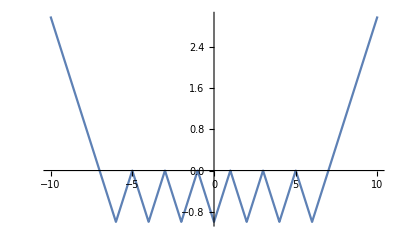

```mathematica
Plot[Nest[Abs[#]-1&,x,7],{x,-10,10}]
```

### 螺旋的切线，法线与副法线

```mathematica
{r1,r2,r3,k}={2,1,0.5,5};
f[u_]:={Cos[u](r1+r2 Cos[k u]),Sin[u](r1+r2 Cos[k u]),r2 Sin[k u]};
b[t_]=Last@FrenetSerretSystem[f[t],t,"Cartesian"];
curve=ParametricPlot3D[f[u],{u,0,2π}];
Manipulate[Show[curve,ParametricPlot3D[f[t]+r3 Cos[u]b[t][[2]]+r3 Sin[u]b[t][[3]],{u,0,2π}],Graphics3D[{Thick,Purple,Arrow[{f[t],f[t]+b[t][[1]]}],Pink,Arrow[{f[t],f[t]+b[t][[2]]}],Magenta,Arrow[{f[t],f[t]+b[t][[3]]}]}]],{{t,1},0,2π}]
```

```mathematica
b[2][[2]]//N
```

{-0.524909,0.629849,0.572503}

```mathematica
ParametricPlot3D[f[u]+Cos[v]b[u][[2]]+Sin[v]b[u][[3]],{u,0,2π},{v,0,2π},RotationAction->"Clip"]
```

$Aborted

```mathematica
{r1,r2,r3,k}={2,1,0.5,5};
x[t_]=Cos[t](r1+r2 Cos[k t]);
y[t_]=Sin[t](r1+r2 Cos[k t]);
z[t_]=r2 Sin[k t];
c[t_]={x[t],y[t],z[t]};
T[t_]=Normalize[c'[t]];
MN[t_]=Normalize[c''[t]];
B[t_]=Cross[T[t],MN[t]];
```

```mathematica
Last@FrenetSerretSystem[c[t],t]/.{t->2}//N
```

{{-0.426182,0.387739,-0.81733},{-0.524909,0.629849,0.572503},{0.736777,0.673014,-0.0649023}}

```mathematica
Cross@@#[[;;2]]==#[[3]]&[%175]
```

True

```mathematica
{T[t],MN[t],B[t]}/.{t->2}//N
```

{{-0.426182,0.387739,-0.81733},{-0.535385,0.639333,0.55192},{0.736547,0.672804,-0.0648821}}

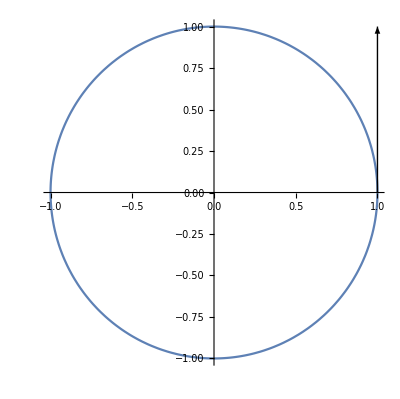

```mathematica
Manipulate[
Show[ParametricPlot[{x[t],y[t]},{t,0,2π}],Graphics[{Arrow[{c[s],c[s]+{-Sin[0],Cos[0]}}]}]],{{s,1},0,2π}]
```

```mathematica
f[t_]:={Cos[t],Sin[t]};
b[t_]=Last@FrenetSerretSystem[f[t],t];
Manipulate[Graphics[{Circle[],Thick,Purple,Arrow[{f[t],f[t]+b[t][[1]]}],Red,Arrow[{f[t],f[t]+b[t][[2]]}]},PlotRange->2],{{t,1},0,2π}]
```

Show::gcomb: 无法合并 Show[,] 中的图形对象.